```mathematica
int = {-0.174250,-0.040052, -0.010779, -0.004119, -0.002032, -0.001115, -0.000639, -0.000364, -0.000289};
err = {0.000062, 0.000040, 0.000024, 0.000014, 0.000009, 0.000004, 0.000005, 0.000028, 0.000079};

i[n_] := Part[int,n];
e[n_] := Part[err,n];
s[n_] := Sum[i[m], {m,1,n}]
es[n_] := Sqrt[Sum[Part[err,m]^2, {m,1,n}]]
r[n_] := i[n]/i[n-1]
naive[n_] := s[n-1]+i[n]/(1-r[n])
nerr[n_] := Sqrt[es[n-2]^2+(i[n-1](i[n-1]-2i[n])e[n-1]/(i[n-1]-i[n])^2)^2 +(i[n-1]^2 e[n]^2/(i[n-1]-i[n])^2)^2]

table = Table[{i[n],e[n],s[n], es[n], If[n>1, naive[n],0], If[n>1, nerr[n],0]},{n,1,9}]//MatrixForm
```

(-0.17425 | 0.000062 | -0.17425 | 0.000062 | 0 | 0
-0.040052 | 0.00004 | -0.214302 | 0.0000737835 | -0.226256 | 0.0000564773
-0.010779 | 0.000024 | -0.225081 | 0.0000775887 | -0.22905 | 0.0000709897
-0.004119 | 0.000014 | -0.2292 | 0.0000788416 | -0.231747 | 0.0000752571
-0.002032 | 9.×10^-6 | -0.231232 | 0.0000793536 | -0.23321 | 0.0000775921
-0.001115 | 4.×10^-6 | -0.232347 | 0.0000794544 | -0.233703 | 0.0000789591
-0.000639 | 5.×10^-6 | -0.232986 | 0.0000796116 | -0.233844 | 0.0000794185
-0.000364 | 0.000028 | -0.23335 | 0.0000843919 | -0.233832 | 0.0000795433
-0.000289 | 0.000079 | -0.233639 | 0.000115598 | -0.234753 | 0.000395837)

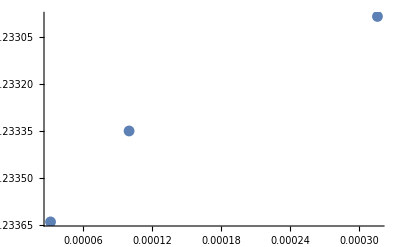

```mathematica
ListPlot[Table[{Sqrt[1/10]^n,s[n]},{n,7,9}], PlotRange -> {-0.51788, -0.51846}]
```

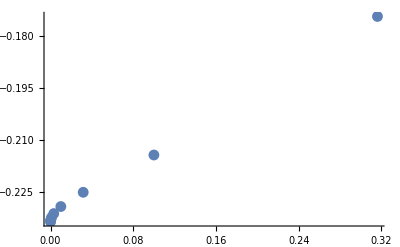

```mathematica
ListPlot[Table[{Sqrt[1/10]^n,s[n]},{n,1,9}], PlotRange -> {-.47, -.52}]
```

```mathematica
data1 = Table[{Sqrt[1/10]^n,s[n]},{n,1,9}];
data2 = Table[{Sqrt[1/10]^n,s[n]},{n,4,8}];
data3 = Table[{Sqrt[1/10]^n,s[n]},{n,4,7}];
```

```mathematica
sqt = Fit[data1, {1, Sqrt[n]},n]
```

-0.237068+0.0995734 √n

```mathematica
line = Fit[data1, {1, n},n]
```

-0.232395+0.184168 n

```mathematica
parabola =  Fit[data1, {1, n, n^2},n]
```

-0.232488+0.192303 n-0.0263697 n^2

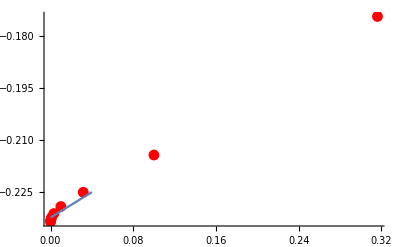

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[line,{n,0,0.04}]]
```

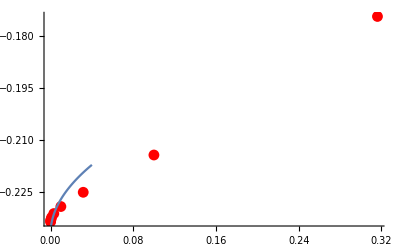

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[sqt,{n,0,0.04}]]
```

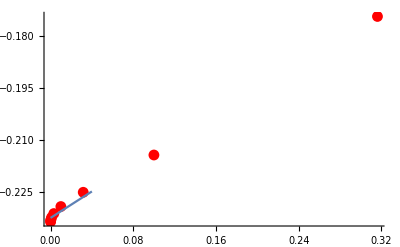

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[parabola,{n,0,0.04}]]
```

```mathematica
cubic =  Fit[data1, {1, n, n^2, n^3},n]
```

-0.232923+0.310877 n-1.64721 n^2+3.95559 n^3

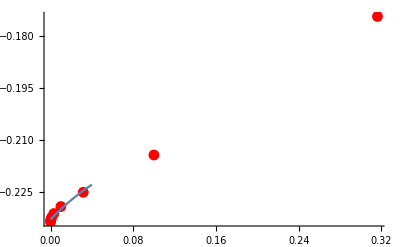

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[cubic,{n,0,0.04}]]
```

-0.233426+0.933657 n-70.626 n^2+2124.47 n^3-19035.5 n^4+41109.5 n^5

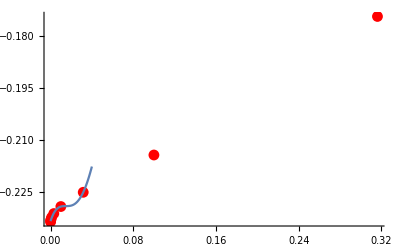

```mathematica
funf=  Fit[data1, {1, n, n^2, n^3, n^4, n^5},n]
Show[ListPlot[data1,PlotStyle->Red],Plot[funf,{n,0,0.04}]]
(*Regress[data1, {1, n, n^2, n^3, n^4, n^5},n,RegressionReport]*)
```

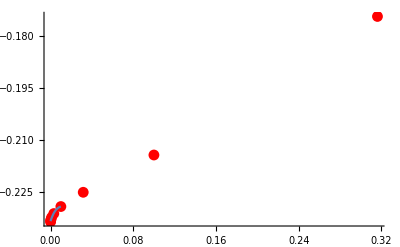

-0.234239+0.140838 √n-7.44289 n+268.063 n^(3/2)-4723.37 n^2+40162. n^(5/2)-146617. n^3+119037. n^(7/2)+281837. n^4-673632. n^5

-Graphics-

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[funf,{n,0,0.01}]]






cmplx =Fit[data1, {1,n^(1/2), n,n^(3/2), n^2,n^(5/2), n^3,n^(6/2), n^4,n^(7/2), n^5},n]
Show[ListPlot[data1,PlotStyle->Red],Plot[funf,{n,0,0.04}]]
```

-0.234667+0.0246569 n^(1/3)

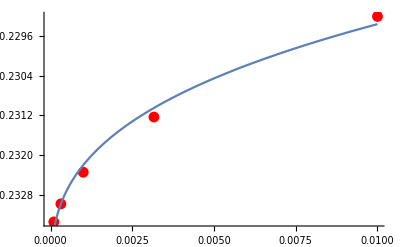

```mathematica
rt3=  Fit[data2, {1,n^(1/3) },n]
Show[ListPlot[data2,PlotStyle->Red],Plot[rt3,{n,0,0.01}]]
```

-0.233809+0.046039 √n

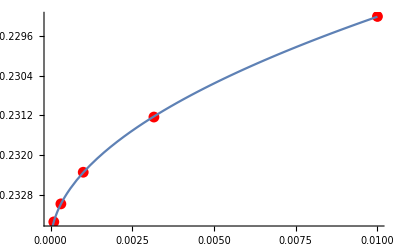

```mathematica
rt2=  Fit[data2, {1,n^(1/2) },n]
Show[ListPlot[data2,PlotStyle->Red],Plot[rt2,{n,0,0.01}]]
```

-0.225791+0.000873279 Log[n]

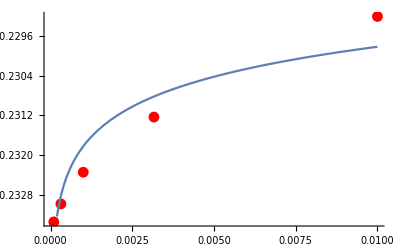

```mathematica
lg2=  Fit[data2, {1,Log[8,n] },n]
Show[ListPlot[data2,PlotStyle->Red],Plot[lg2,{n,0,0.01}]]
```

-0.233807+0.0460197 √n

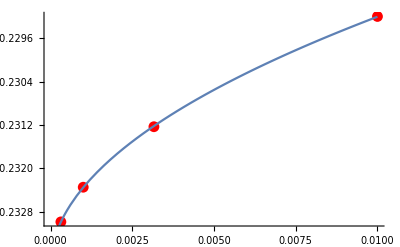

```mathematica
rtt2=  Fit[data3, {1,n^(1/2) },n]
Show[ListPlot[data3,PlotStyle->Red],Plot[rtt2,{n,0,0.01}]]
```

```mathematica
par3=  Fit[data3, {1,n^(1/2) },n]
Show[ListPlot[data3,PlotStyle->Red],Plot[par3,{n,0,0.01}]]
```

-0.233807+0.0460197 √n

-Graphics-